```mathematica
session = StartExternalSession["Python-NumPy"]
```

ExternalSessionObject[…]

```mathematica
ExternalEvaluate[session, "import os; import sys"]
ExternalEvaluate[session, 
<| "Command" -> "os.chdir",
"Arguments" -> {NotebookDirectory[]} |>]
ExternalEvaluate[session, 
<| "Command" -> "sys.path.append",
"Arguments" -> {NotebookDirectory[]} |>]
ExternalEvaluate[session, "import plsa"]
ExternalEvaluate[session, "import torch"]
ExternalEvaluate[session, "import numpy"]
```

```mathematica
Timing[plsa$result =ExternalEvaluate[session, <|
"Command" -> "plsa.run_plsa_numpy",
"Arguments" -> {
RandomReal[{0,10}, {1000, 10}],
10,
100}
|>];]
plsa$result//Keys
```

{0.203125,Null}

{pz,pxi_given_zs,pz_given_xi,loglik}

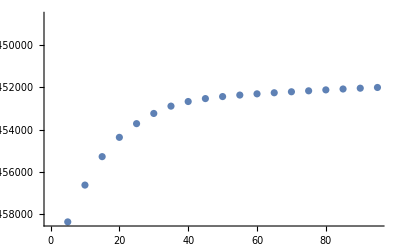

```mathematica
ListPlot[plsa$result["loglik"]]
```

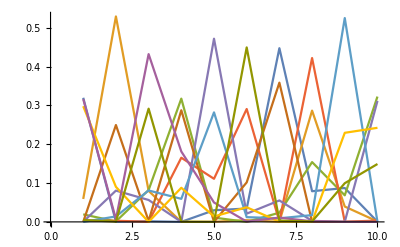

```mathematica
ListLinePlot[plsa$result["pz_given_xi"][[2]]ᵀ]
```